## Differences between primes

```mathematica
results={};n=3;primes=allPrimes[[n]];
```

## Prime 3

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
g3=Graph[visibles[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gv3=Overlay[{g3,Style["d=3", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igv3=Graph[visibles, VertexLabels->"Name",VertexLabelStyle->Large,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv3];
```

```mathematica
count = Total[adj]//Counts
```

<|31→16,30→6,28→14,26→16,23→31,29→11,24→20,27→15,21→43,20→38,32→9,43→3,36→5,37→5,52→4,53→1,49→2,98→1,50→2,47→2,70→1,79→1,99→1,87→1,77→2,125→1,156→1,128→1,189→1,22→29,15→84,19→46,10→276,6→922,14→125,12→172,8→483,9→389,4→1603,3→1946,18→64,2→1203,16→78,13→143,7→634,5→1185,17→74,11→226,39→4,42→3,33→5,25→17,35→7,34→5,38→4,40→2,45→3,61→1,62→1,80→1,67→1,51→3,54→1,55→1,41→1,46→1,44→2|>

```mathematica
Sort[count]
```

<|53→1,98→1,70→1,79→1,99→1,87→1,125→1,156→1,128→1,189→1,61→1,62→1,80→1,67→1,54→1,55→1,41→1,46→1,49→2,50→2,47→2,77→2,40→2,44→2,43→3,42→3,45→3,51→3,52→4,39→4,38→4,36→5,37→5,33→5,34→5,30→6,35→7,32→9,29→11,28→14,27→15,31→16,26→16,25→17,24→20,22→29,23→31,20→38,21→43,19→46,18→64,17→74,16→78,15→84,14→125,13→143,12→172,11→226,10→276,9→389,8→483,7→634,6→922,5→1185,2→1203,4→1603,3→1946|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[;;-2]];
```

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.413716/x^1.07386]

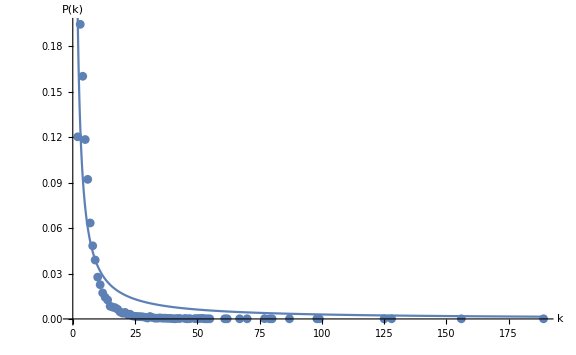

```mathematica
vis3=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-3.eps",vis3];
```

## Mean degree

```mathematica
degree=VertexDegree[igv3]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n, Length@diffs,degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
h3=Graph[horizontals[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gh3=Overlay[{h3,Style["d=3", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igh3=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle->Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh3];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,2→3355,3→2218,4→1542,5→941,6→643,9→198,7→415,8→280,11→87,10→131,12→72,14→29,19→2,13→44,15→17,16→7,18→2,17→12,20→2,25→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,305/909},{3,2218/9999},{4,514/3333},{5,941/9999},{6,643/9999},{9,2/101},{7,415/9999},{8,280/9999},{11,29/3333},{10,131/9999},{12,8/1111},{14,29/9999},{19,2/9999},{13,4/909},{15,17/9999},{16,7/9999},{18,2/9999},{17,4/3333},{20,2/9999},{25,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

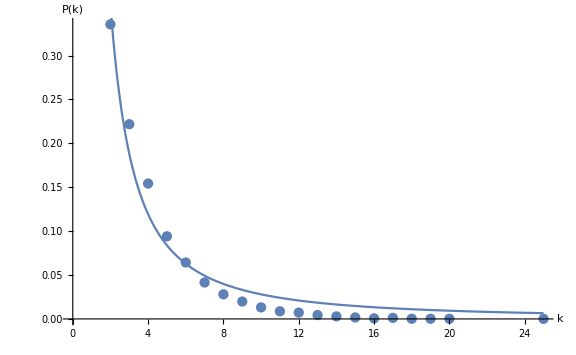

```mathematica
hvis3=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-3.eps",hvis3];
```

## Mean degree

```mathematica
degree=VertexDegree[igh3]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n, Length@diffs,degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,3,500,6.776,0.984145 ± 0.236521,0.37697 ± 0.130101},{horizontal,3,500,3.844,1.54823 ± 0.28404,1.05328 ± 0.304314}}